## 6D_1 GRW Solutions

Case 6D_1 :  4D spacetime (t,r,θ,ϕ) + two individually curled axis (ψ)
Time metric:  A(t,r) dt^2
3-space metric:  -a[t]^2Β[r) dr^2 – a(t)^2ℭ(r) r^2 dθ^2 – a(t)^2ℭ(r) r^2sin^2θ  dϕ^2
_1: Curled geometry:  Product of two circles (radii p_4 and p_5) (S^1 x S^1)
     Curled metric :  -a[t]^2 𝔇_4[r] p_4^2 dψ_4^2  – a[t]^2 𝔇_5[r] p_5^2 dψ_5^2

### Notation

Greek indices (μ,ν,γ,δ) range from dimL to dimH and are used for functions
Latin indices (i,j,k,m,n) range from 1 to numDim and are used for matrices, also called tables or sequences in Mathematica
 
			Function      Matrix
Example 1:                0–3          1–4             Spacetime
Example 2:               1-3          1–3        3-space
Example 3:               2-3          1–2           yz-plane

gMat = contravariant metric tensor g_μν in matrix form: gMat[[m,n]]
g = contravariant metric tensor as a  function :   g[μ,ν]
GMat = covariant metric tensor g^μν in matrix  form : GMat[[m,n]]
G = covaiant metric tensoras a  function :   G[μ,ν]  

Matrices in Mathematica have subscripts 1-N and require[[...]]
Spacetime functions are given subscripts 0-3 and just use[...]
delDim = dimL – 1   
m = μ – delDim       n = ν – delDim
Used to convert indices between functions and matrices 

 Γ_νγ^μ = Connection Coefficient of 1st kind  
 Γ_(δ⋁γ) = Connection Coefficient of 2nd kind 
 Γ_νγ^μ = Σ_δ g^μδ Γ_(δ⋁γ) , a sum over δ 
Γ[μ,ν,γ] ≡ Γ_νγ^μ 
G[μ,δ] ≡ g^μδ  
Γδνγ[ν,γ,δ] ≡ Γ_(δ⋁γ)
Γ[μ,ν,γ] = Σ_δ G[μ,δ] Γδνγ[ν,γ,δ]

Γ_(δ⋁γ) = 1/2(∂_ν g_δγ + ∂_γ g_νδ – ∂_δ g_νγ)
Γδνγ[ν,γ,δ]= 1/2(D[g[δ,γ],x^ν] + D[g[ν,δ],x^γ] – D[g[ν,γ],x^δ])  

Γ[μ,ν,γ,δ] ≡ g^μδ Γ_(δ⋁γ)  (for a fixed δ)
Γ[μ,ν,γ,δ] = G[μ,δ] Γδνγ[ν,γ,δ]
Γ[μ,ν,γ] = Σ_δ Γ[μ,ν,γ,δ]  

 R_μν = Ricci Tensor 
 RMat = R_μνσ^σ is a table  (or matrix)  of Ricci tensors R_μν
 RMat[[m,n]] ≡ R[μ,ν]    (R  is a function)
   = ∑_σ [∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ + ∑_ρ (Γ_μσ^ρ Γ_ρν^σ – Γ_μν^ρ Γ_ρσ^σ)] 
 ΓΓ[μ,ν,σ] ≡ ∑_ρ (Γ_μσ^ρ Γ_ρν^σ – Γ_μν^ρ Γ_ρσ^σ)
  R[μ,ν] = ∑_σ [∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ + ΓΓ[μ,ν,σ]

### Reset Variables

```mathematica
ClearAll["Global`*"];
Clear[Derivative]

(*ClearAll only cleans variables belonging to the Global context. Derivatives belong to the System context. So, in order to clear, say, A[t,r] and A'[t,r], need both of the lines above.*)

Clear[Subscript]  (* Clears Subscript[𝔇, 4], Subscript[𝔇, 5], ... *)
Clear[K];  (*  K is the default summation index and requires a specific Clear. *)

Off[InverseFunction::ifun];(* Disables warning message that 'some inverses may be lost' when solving *)
(* Subscript[g, 00]=1 for a(t). Presumably a(t) is a monotonic function and so the inverse *)
(* is unique. *)
```

### Output Controls

Default flag values are zero
flag1 = 0 means to skip the multiplication check for metric tensor matrices
           = 1 means to include the matrix check in the output
flags 2-7 =0 means to only output data for non-zero terms 
                 = 1 means to output data for all terms, zero and non-zero

```mathematica
flag1  = 0;  (* Print the multiplication check for metric tensor matrices  *)
flag2  = 0;  (* Print the three ∂_α Subscript[g, βγ] terms that make up Subscript[Γ, δνγ] *)
flag3  = 0;  (* Print table of all Subscript[Γ, δνγ], (for both zero and non-zero) *)  
flag4  = 0;  (* Print the four δ terms that sum to Subscript[Γ, νγ]^μ, for all Subscript[Γ, νγ]^μ *)
flag5  = 0;  (* Print table of all Subscript[Γ, νγ]^μ (both zero and non-zero) *)  
flag6  = 0;  (* Print Computational Steps for all Subscript[R, μν], both zero and non-zero  *)
flag7  = 0;  (* Print table of all Subscript[R, μν], both zero and non-zero  *)
```

#### Rules

```mathematica
(*  Rules Inputs   *)
(* Rules      Used to simplify output displays. 
e.g., θ'' -> θ̈ in geodesic eqs  *)

rulesDisp={Derivative[y_,0][x_][_,_]:>OverDot[x,y],Derivative[0,1][x_][_,_]:>x',Derivative[0,2][x_][_,_]:>x'',Derivative[0,3][x_][_,_]:>x''',Derivative[y_,1][x_][_,_]:>OverDot[x,y]',(v:A|B|ℂ|Subscript[𝔻, _])[_,_]:>v,Derivative[y_][x_][t]:>OverDot[x,y],Derivative[y_][x_][τ]:>OverDot[x,y],Derivative[y_][x_][𝕥]:>OverDot[x,y],x_'[r_]:>x',x_''[r_]:>x'',(v:a|𝒜|ℬ|𝒞|Subscript[𝒟̂, _]|Subscript[𝒟, _]|ℱ|𝒻|Α|Β|ℭ|Subscript[𝔇̂, _]|Subscript[𝔇, _]|𝔉|𝔣)[_]:>v};
	 (* Simplifies display of metric tensors and their derivatives *)

rulesX={𝓍'[0]->ṫ,𝓍'[y_]->OverDot[𝓍[y],1],𝓍''[0]->ẗ,𝓍''[y_]->OverDot[𝓍[y],2]}; ;
(* This generates coordinate derivatives like t^(..) &θ^(..) in the spacetime geodesic equations.  *)

rulesDot={Derivative[y_][a_][t]:>OverDot[a,y][t],Derivative[y_][a_][τ]:>OverDot[a,y][τ]};
(* This replaces terms like a'[t] and 𝒜'[t] with ȧ[t] and 𝒜̇[t] *)

(* Any of the rules below, if used, must precede ruleDisp *)
rulesK12={K[1]->K[2]}; (* Change first integral when two answers have integrals *)
rulesKr={K[1]->ρ,K[2]->σ,K[_]->ω};  (* makes antiderivatives wrt r more readable *)
rulesKt={K[x_]->τ};  (* makes antiderivatives wrt t more readable *)
```

### Inputs

```mathematica
(* Coordinates. *)
dimL=0;dimH=5;  (* Low and High manifold dimensions  *)
𝓍[0]=t;   (*  Script x on LHS is a different symbol than x *)
𝓍[1]=r;  
𝓍[2]=θ; 
𝓍[3]=ϕ;
𝓍[4]=Subscript[ψ, 4];
𝓍[5]=Subscript[ψ, 5]; 
(*  Note script x!  Can enter Esc scx Esc 
    Want to reserve regular x for Cartesian coordinates *)

(* Metric tensor matrix g = Subscript[g, μν] *)
gMat={{A[t,r],0,0,0,0,0},{0,-a[t]^2 Β[r],0,0,0,0},{0,0,-a[t]^2 ℭ[r] r^2,0,0,0},{0,0,0,-a[t]^2 ℭ[r] r^2 Sin[θ]^2,0,0},{0,0,0,0,-a[t]^2 Subscript[p, 4]^2,0},{0,0,0,0,0,-a[t]^2 Subscript[𝔇, 5][r] Subscript[p, 5]^2}}; 

(* Case Description" *)
case:=Style[Column[{
Row[{"Starting Metric: g_00=",gMat[[1,1]]/.rulesDot,", g_11=",gMat[[2,2]],", g_22=",gMat[[3,3]],","}],
Row[{"g_33=",gMat[[4,4]],", g_44=",gMat[[5,5]],", g_55=",gMat[[6,6]],","}],Row[{"a(t) not constant"}]}],13]

(* Labels for table titles 
	Typically i,j,k,ℓ or A,B,C,D, or μ,ν,γ,δ *)
index1="μ"; index2="ν";  index3="γ";
index4="δ";index5="σ";index6="ρ";
```

#### Notes

Mathematica bug sometimes confuses superscript double primes and 2nd derivative double primes, so must put A''[r] in quotes

Also, when doing replacements like x+y /. x:>z,  it is generally necessary to put derivatives of subscripted variables in quotes 
	e.g., use /. D[k_1[r],r] → "k_1'"  or else expressions like k_1'/k_1 cause a mess 
	I avoid this need for quotes: 
	     For example,  instead of using k_1'[r] in rulesDisp, I use  x_'[r]:>x'  
	     where x_ stands for any parameter

Clear[K] works but Clear[K_1] gives an error message that K_1 is not a variable
Must either use Clear[Subscript] to clear all subscripted variables or K_1=. to clear just K_1

It is OK to use the same symbol for a constant, one  variable, and two variables
It is also OK to set A[t,r] = A[t], but  not OK to set  A[t]=A, a constant
     Because if later set A=1, then Mathematica displays A[t] as 1[t] . 
     In general, to be safe from such idiosyncrasies, I use different fonts for the symbols: 
          Regular A[t,r], double-strike ℂ[t,r],  script 𝒜[t], Greek Α[r] or Gothic ℭ[r]
          I use symbols like  k or Greek α  for constants.  
          So, 𝒜[t] = α and later α=1 is OK.

Mathematica generally uses  K[1] for the integration dummy variable.
     To make integrals easier to read, I use rulesKr   or  rulesKt 
          This changes, for example, Β[K[1]] dK[1]  to  Β[ρ] dρ    or   𝒜[K[1]] dK[1]  to  𝒜[τ] dτ
     Don't use K as a free constant. If later set K=3, then dummy variable K[1] → 3[1]

For double integrals, Mathematica generally uses K[2] for the outer dummy variable and K[1] for the inner dummy variable.
     To make this readable, I use the substitution /.rulesKKr

Warning: for readability of integrals, put /.rulesKr or /.rulesKt before /.rulesDisp
     This makes  expressions with functions of ρ, σ, and τ more readable
     For example, ⅇ^(-1/2 (-4/σ+Β'/Β-(2 "𝔇_4''")/𝔇_4'-(4 Β (-2 c^2+k Λ 𝔇_4))/(k 𝔇_4')-𝔇_4'/𝔇_4)ρ1r)
     Caution: Mathematica now considers all of these symbols to be constants
     For very simple expressions, Mathematica erroneously integrates the 'constants'
          If that happens, must omit /.rulesDisp. The expressions should be almost as readable
          For example, might get  ∫_1^r   2Β'[ρ]𝔇_4[ρ] dρ  rather than the desired ∫_1^r   2 Β' 𝔇_4 dρ

### Define Metric Tensor Functions

```mathematica
GMat=Simplify[Inverse[gMat]];   
(* GMat must be a deferred definition so that refinements to Subscript[R, μν] can be tested using gMat. Ditto for definitions of Subscript[Γ, μνσ], Subscript[Γ, νσ]^μ, 
and Subscript[R, μν]. *)   
identity=Simplify[GMat.gMat];

delDim=dimL-1;
g[μ_,ν_]:=gMat[[μ-delDim,ν-delDim]];  
(* Converts matrix g to function g *)
G[μ_,ν_]:=GMat[[μ-delDim,ν-delDim]];
```

### Create Table Template Functions

```mathematica
(* Zero-One function 
zero1(x)=1 if x≠0  
zero1(x)=0 if x=0
Used to reduce tables to only display non-zero output   *)
zero1[x_]:=Module[{xval},xval=1;If[x==0,xval=0];xval];  

(* Variables related to dimension of manifold *)
numDim=1+dimH-dimL;  (* Number of dimensions *)
 colorDim=numDim; (* Table color changes after numDim rows
For example: 100, 101, 102, 103 is a block of same color *) 

(* 2-Parameter Tables *)
table2[title_,text1_,text2_,textF_,column1_,column2_,columnF_,colorDim_]:=
Column[{title,Style[Grid[Transpose@{column1,column2,columnF}~Prepend~
{text1,text2,textF},
Dividers->All,ItemStyle->{Automatic,{{Bold,Black},Join[Table[Blue,colorDim],
Table[Magenta,colorDim]]}},Alignment->{Left,"."}],FontSize->16]}];

column21={};  (* column 1: 0,0,0,0,1,1,1,1, ...  *)
For[dim=dimL,dim≤dimH,dim++,column21=Join[column21,Table[dim,numDim]]];
column22=Flatten[Table[Table[ν,{ν,dimL,dimH}],numDim]];
(*column2: 0,1,2,3,0,1,2,3, ...*)

(* 3-Parameter Tables *)
table3[title_,text1_,text2_,text3_,textF_,column1_,column2_,column3_,columnF_,
colorDim_]:=
Column[{title,Style[Grid[Transpose@{column1,column2,column3,columnF}~Prepend~
{text1,text2,text3,textF},Dividers->All,ItemStyle->
{Automatic,{{Bold,Black},Join[Table[Blue,colorDim],Table[Magenta,colorDim]]}},
Alignment->{Left,"."}],FontSize->16]}];

column31={};  (* column 1: 16 zeros, then 16 ones, then twos, then threes *)
For[dim=dimL,dim≤dimH,dim++,column31=Join[column31,Table[dim,numDim^2]]];
column32={};  (* column 2: 4 zeros, then ones-twos-threes, done 4 times *)
For[dim=dimL,dim≤dimH,dim++,column32=Join[column32,Table[dim,numDim]]];
column32=Flatten[Table[column32,numDim]];
column33=Table[σ,{σ,dimL,dimH}];  (* column 3: 0,1,2,3 over and over *)
column33=Flatten[Table[column33,numDim^2]];
```

### Line Element Output

```mathematica
lineElem:=Module[{firstElem,fourterms,kount,kount4,line,gμν,gzero,xμ,xν,
negSign,factor,plus,posTerm,Lparen,Rparen,nextTerm,lineElem},

fourterms="";
firstElem=1;
kount=0;  (* Counter of terms being printed *)
kount4=0; (* Counter of # of rows to output*)
For[μ=dimL,μ≤dimH,μ++,
For[ν=dimL,ν≤dimH,ν++,
If[g[μ,ν]===0,gzero=0,gzero=1,gzero=1]; (* 1 means Subscript[g, μν]≠0 *)

If[gzero==1,  (* If there is a non-zero Subscript[g, μν] term to print *)
kount=kount+1;  (* Increment # of terms being printed (4 per row) *)
(*Print["μ, ν, kount: ",μ,", ",ν,", ",kount];*)

gμν=g[μ,ν];
(*Print["gμν = ",gμν]
Print["𝓍[ν], 𝓍ν = ",𝓍[ν],", ",ToString[𝓍[ν]//OutputForm]];*)
xμ=ToString[𝓍[μ]];
xν=ToString[𝓍[ν]];

negSign=Module[{e=Expand[gμν],lead},
   lead=If[Head[e]===Plus,First[e],e];
   TrueQ[lead/.{Times[k_?NumericQ,___]:>k<0,k_?
NumericQ:>k<0,_:>False}]];
   (* True if the leading term of the expanded gμν is negative; handles ±1 too *)

factor=1;
	(* Factor to prevent gμν from being negative in nextTerm *)

If[negSign===True,
plus=" - ";factor=-1,
plus=" + "];
If[firstElem==1,firstElem=0;gμν=g[0,0];If[plus==" + ",plus=""]];
	(* Suppress + sign on a first term that is positive *)
If[gμν==1,gμν=""];
posTerm=factor gμν/.Times[-1,x___,p_Plus,y___]:>Times[x,Expand[-p],y];
   (* move a leftover minus into a sum: -(p.b2(-1-x)) -> p.b2(1+x) *)

Lparen="";
Rparen="";
If[Head[gμν]==Plus,Lparen="("]; (* Put sums like -r^2+α in parentheses *)
If[Head[gμν]==Plus,Rparen=")"];
nextTerm=Row[{Lparen,posTerm,Rparen," d",𝓍[μ]," d",𝓍[ν]}]; 
			(* Next off-diagonal line element term *)
If[μ==ν,nextTerm=Row[{Lparen,posTerm,Rparen," d",𝓍[μ]^2}]]; 
			(* Next diagonal line element term *)
(*Print["nextTerm = ",nextTerm];*)

If[Mod[kount,4]==1,
kount4=kount4+1;
line[kount4]=""];  (* Initialize new row = ϕ *)
(*Print["kount4 = ",kount4];*)

If[kount4*kount==1,
line[kount4]=Row[{"ds^2 = ",plus,nextTerm}], (* ds^2 only on row 1 *)
line[kount4]=Row[{line[kount4],plus,nextTerm}]];  (* Else, append new term *) 

(*Print["line(",kount4,") = ",line[kount4]];*)
lineElem=If[kount4==1,line[1],Column[Table[line[i],{i,kount4}]]]]]];
lineElem] 
(* end of module *)

lineElem/.rulesDot(*  write line element  *)
```

ds^2 = A[t,r] dt^2 - a[t]^2 Β[r] dr^2 - r^2 a[t]^2 ℭ[r] dθ^2 - r^2 a[t]^2 Sin[θ]^2 ℭ[r] dϕ^2
 - a[t]^2 p_4^2 dψ_4^2 - a[t]^2 p_5^2 𝔇_5[r] dψ_5^2

### Output Message about dot and prime

```mathematica
line2="Output Display Simplification – Parameters are sometimes suppressed";
line3="   Prime (') means derivative wrt r.";
line4="   Dot (.) means derivative wrt t."; 
aDot=Style[OverDot[A],Bold,Brown];
line5=Row[{"   Examples: A = A(t,r),  A'=∂_r A(t,r) and ",aDot,
	"=∂_t A(t,r) "}];
caseMsg:=Column[{case,"","Corresponding Line Element",lineElem,"",line2,line3,
	line4,line5}];
caseMsg
```

Starting Metric: g_00=A[t,r], g_11=-a[t]^2 Β[r], g_22=-r^2 a[t]^2 ℭ[r],
g_33=-r^2 a[t]^2 Sin[θ]^2 ℭ[r], g_44=-a[t]^2 p_4^2, g_55=-a[t]^2 p_5^2 𝔇_5[r],
a(t) not constant

Corresponding Line Element
ds^2 = A[t,r] dt^2 - a[t]^2 Β[r] dr^2 - r^2 a[t]^2 ℭ[r] dθ^2 - r^2 a[t]^2 Sin[θ]^2 ℭ[r] dϕ^2
 - a[t]^2 p_4^2 dψ_4^2 - a[t]^2 p_5^2 𝔇_5[r] dψ_5^2

Output Display Simplification – Parameters are sometimes suppressed
   Prime (') means derivative wrt r.
   Dot (.) means derivative wrt t.
   Examples: A = A(t,r),  A'=∂_r A(t,r) and Ȧ=∂_t A(t,r)

### Metric Tensor Matrices Output

```mathematica
matrixg=Row[{"g: (g_μν) = ",MatrixForm[gMat]}]/.rulesDisp;
matrixG=Row[{"G: (g^μν) = ",MatrixForm[GMat]}]/.rulesDisp;
iden=Row[{"Check: G.g = ",MatrixForm[identity]}];
matrixout=Column[{matrixg,"",matrixG}];
If[flag1==1,matrixout=Column[{matrixg,matrixG,iden}]];
matrixout
```

g: (g_μν) = (A | 0 | 0 | 0 | 0 | 0
0 | -a^2 Β | 0 | 0 | 0 | 0
0 | 0 | -a^2 r^2 ℭ | 0 | 0 | 0
0 | 0 | 0 | -a^2 r^2 ℭ Sin[θ]^2 | 0 | 0
0 | 0 | 0 | 0 | -a^2 p_4^2 | 0
0 | 0 | 0 | 0 | 0 | -a^2 p_5^2 𝔇_5)

G: (g^μν) = (1/A | 0 | 0 | 0 | 0 | 0
0 | -1/(a^2 Β) | 0 | 0 | 0 | 0
0 | 0 | -1/(a^2 r^2 ℭ) | 0 | 0 | 0
0 | 0 | 0 | -Csc[θ]^2/(a^2 r^2 ℭ) | 0 | 0
0 | 0 | 0 | 0 | -1/(a^2 p_4^2) | 0
0 | 0 | 0 | 0 | 0 | -1/(a^2 p_5^2 𝔇_5))

### g^μν Table Output

```mathematica
titleT=("Table of g")^Style[Row[{index1, index4}],Bold,Blue];
column2F= Flatten[GMat];
titleg=("g")^Style[Row[{index1, index4}],Bold,Blue]; 
table2[titleT,index1,index4,titleg,column21,column22,column2F/. rulesDisp,
numDim]
```

### Compute Γ_(δ⋁γ) = 1/2(∂_ν g_δγ + ∂_γ g_νδ – ∂_δ g_νγ)

```mathematica
Γδνγ[ν_,γ_,δ_]:=1/2(
D[g[δ,γ],𝓍[ν]]+D[g[ν,δ],𝓍[γ]]-D[g[ν,γ],𝓍[δ]]); 

gammaδνγ=Table[Γδνγ[ν,γ,δ],{ν,dimL,dimH},{γ,dimL,dimH},{δ,dimL,dimH}];
dell=Style[ 𝜕,Bold,FontSize->22];  (* ∂ with its Font size *)
gSize=12;  (* Font size of g *)
```

### Print the 3 terms that sum to Γ_δνγ (debug)

```mathematica
dell=Style[ 𝜕,Bold,FontSize->22];  (* ∂ with its Font size *)
gSize=12;  (* Font size of g *)
titleg=Style[Row[{Subscript["Computation of terms that sum to Γ", Row[{index4,index2,index3}]],
" = 1/2(",Subscript[dell, index2],Subscript["g", Row[{index4,index3}]],
" + ",Subscript[dell, index3], Subscript["g", Row[{index2,index4}]]," – ",Subscript[dell, index4], Subscript["g", Row[{index2,index3}]],")"}],
Bold,Blue,gSize];

titleg

For[δ=dimL,δ≤1,δ++,For[ν=dimL,ν≤1,ν++,For[γ=dimL,γ≤2,γ++,
(* Summary row for Subscript[Γ, δνγ] at top *)
TFHead=(Head[Γδνγ[δ,ν,γ]]===Integer);
If[flag2==1,TFHead=False];
If [TFHead==False, (*i.e. Subscript[Γ, δνγ] ≠ integer *)
Print[index4, "=", δ, "  ", index2, "=", ν, "  ", index3, 
  "=", γ, Subscript[":  2 Γ", Row[{δ,ν,γ}]]," = " ,2Expand[Γδνγ[ν,γ,δ]]/.rulesDisp];

(* The three terms on RHS of Subscript[Γ, δ⋁γ] = 1/2(∂_ν Subscript[g, δγ] + ∂_γ Subscript[g, νδ] – ∂_δ Subscript[g, νγ]) *)  
Print[Subscript["    ∂", 𝓍[ν]],Subscript["g", Row[{δ,γ}]], Subscript[" = ∂", 𝓍[ν]],"(",g[δ,γ],") = ",
D[g[δ,γ],𝓍[ν]]/.rulesDisp];
Print[Subscript["    ∂", 𝓍[γ]],Subscript["g", Row[{ν,δ}]],Subscript[" = ∂", 𝓍[γ]],"(",g[ν,δ],") = " ,D[g[ν,δ],𝓍[γ]]
/.rulesDisp];
Print[Subscript["   -∂", 𝓍[δ]],Subscript["g", Row[{ν,γ}]], Subscript[" = -∂", 𝓍[δ]],"(",g[ν,γ],") = -(",D[g[ν,γ],𝓍[δ]]
/.rulesDisp,")"];
Print[];
]]]];
```

### Γ_δνγ Table Output

```mathematica
column3F=Flatten[gammaδνγ];
If[flag3==1,titleT=Style[Row[{Subscript["Table of all Γ", Row[{index4,index2,index3}]],
" = 1/2(",Subscript[dell, index2],Subscript["g", Row[{index4,index3}]],
" + ",Subscript[dell, index3], Subscript["g", Row[{index2,index4}]]," – ",Subscript[dell, index4], Subscript["g", Row[{index2,index3}]],")"}],
Bold,Blue,gSize],

titleT=Style[Row[{Subscript["Table of non-zero Γ", Row[{index4,index2,index3}]],
" = 1/2(",Subscript[dell, index2],Subscript["g", Row[{index4,index3}]],
" + ",Subscript[dell, index3], Subscript["g", Row[{index2,index4}]]," – ",Subscript[dell, index4], Subscript["g", Row[{index2,index3}]],")"}],
Bold,Blue,gSize];
];

titleg=Style[Subscript["Γ", Row[{index4,index2,index3}]],Bold,Blue,gSize];

If[flag3==1,  (* table of all Γδνγ terms *)
table3[titleT,index4,index2,index3,titleg,column31,column32,column33,column3F
/.rulesDisp,numDim]]

If[flag3==0,    (* table of non-zero Γδνγ terms  *)
column01=zero1/@column3F;
column1=column31/.{0->-1};
column1=Cases[column01*column1,Except[0]]/.{-1->0};
column2=column32/.{0->-1};
column2=Cases[column01*column2,Except[0]]/.{-1->0};
column3=column33/.{0->-1};
column3=Cases[column01*column3,Except[0]]/.{-1->0};
columnF=Cases[column3F,Except[0]];
table3[titleT,index4,index2,index3,titleg,column1,column2,column3,columnF
/.rulesDisp,1]] 
(* Last entry of "1" changes table from blocks of text color to alternate 
row colors due to unpredictable pattern of non-zero terms*)
```

### Compute Γ_νγ^μ = g^μδ Γ_δνγ

```mathematica
Γ[μ_,ν_,γ_,δ_]:=Simplify[G[μ,δ] Γδνγ[ν,γ,δ]]; 
Γ[μ_,ν_,γ_]:=Simplify[Sum[ Γ[μ,ν,γ,δ],{δ,dimL,dimH}]];  
gammaμνγ=Table[Γ[μ,ν,γ],{μ,dimL,dimH},{ν,dimL,dimH},{γ,dimL,dimH}];
```

### Print Γ_νγ^μ computational steps (debug)

```mathematica
Print["Backup Data: Computation of ",Style[Row[{Subscript[Γ, Row[{index2, index3}]]^index1,
(" = g")^Row[{index1,index4}],Subscript["Γ", Row[{index4,index2,index3}]]}],Bold,Blue]];
For[μ=dimL,μ≤dimL+1,μ++,
For[ν=dimL,ν≤dimL+1,ν++,
For[γ=dimL,γ≤dimL+2,γ++,
TFHead=(Head[Γ[μ,ν,γ]]===Integer);
If[flag4==1,TFHead=False]; (* if want to print all cases  *)
If [TFHead==False, (*i.e. Subscript[Γ, νγ]^μ ≠ integer (=0) *)

(* Summary row for Subscript[Γ, νγ]^μ at top *)
Print[index1, "=", μ, "  ", index2, "=", ν, "  ", index3, 
  "=", γ, Subscript[":  Γ", Row[{ν,γ}]]^Text[μ], " = " ,Expand[Γ[μ, ν, γ]]/.rulesDisp];

(* Four rows showing terms that add to Subscript[Γ, νγ]^μ *)
For[δ= dimL,δ≤dimH,δ++,
Print[index4,"=",δ,(": g")^Row[{μ,δ}],Subscript["Γ", Row[{δ,ν,γ}]]," = (",G[μ,δ]/.rulesDisp,
")(",Expand[Γδνγ[ν,γ,δ]]/.rulesDisp,") = ",Expand[Γ[μ,ν,γ,δ]]
/.rulesDisp];  

];Print[]];
]]]
```

### Γ_νγ^μ Table Output

```mathematica
If[flag5==1,titleT1="Table: All values of ",titleT1="Table: Non-zero values of "];  

titleT=Style[Row[{titleT1,Subscript[Γ, Row[{index2, index3}]]^index1,(" = g")^Row[{index1,index4}],
"[",("1/2(∂")_index2,Subscript["g", Row[{index4,index3}]],Subscript[" + ∂", index3],Subscript["g", Row[{index2,index4}]],
Subscript[" – ∂", index4],Subscript["g", Row[{index2,index3}]],(")] = g")^Row[{index1,index4}] Subscript[Γ, Row[{index4,index2,index3}]]
}],Bold,Blue];(* Title above table *)

indexF=Style[Subscript[Γ, Row[{index2, index3}]]^index1,Bold,Blue];   (* Subscript[Γ, νγ]^μ *)
column3F=Flatten[gammaμνγ];

If[flag5==1,  (* table of all values of Subscript[Γ, νγ]^μ  *)
table3[titleT,index1,index2,index3,indexF,column31,column32,column33,column3F
/.rulesDisp,numDim]]

If[flag5==0,  (* table of non-zero values of Subscript[Γ, νγ]^μ  *)
column01=zero1/@column3F;
column1=column31/.{0->-1};
column1=Cases[column01*column1,Except[0]]/.{-1->0};
column2=column32/.{0->-1};
column2=Cases[column01*column2,Except[0]]/.{-1->0};
column3=column33/.{0->-1};
column3=Cases[column01*column3,Except[0]]/.{-1->0};
columnF=Cases[column3F,Except[0]];
colorDim=1; (* Changes table to alternate row colors due to unpredictable pattern of non-zero terms *)

table3[titleT,index1,index2,index3,indexF,column1,column2,column3,columnF
/. rulesDisp,1]]
```

### Compute R_μν

```mathematica
xS[x_]:=Expand[Simplify[x]];
xF[x_]:=Expand[FullSimplify[x]];

ΓΓ[μ_,ν_,σ_]:=Simplify[Sum[Γ[ρ,μ,σ] Γ[σ,ρ,ν]-Γ[ρ,μ,ν] Γ[σ,ρ,σ],{ρ,dimL,dimH}]];

R[μ_,ν_]:=
xS[Sum[D[Γ[σ,μ,σ],𝓍[ν]]-D[Γ[σ,μ,ν],𝓍[σ]]+ ΓΓ[μ,ν,σ],{σ,dimL,dimH}]];

RMat=Table[R[μ,ν],{μ,dimL,dimH},{ν,dimL,dimH}];
column2F=Flatten[RMat]; (* Subscript[R, μν]-column values, stored as a list  *)

indexr=Style[Row[{Subscript["R",Row[{index1,index2}]]}],Bold,Blue];
indexR=Style[Row[{Subscript["R",Row[{index1,index2}]],
" = ∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ + Γ_μσ^ρΓ_ρν^σ – Γ_μν^ρΓ_ρσ^σ"}],Bold,Blue];
```

### Print computational steps for R_μν (debug)

```mathematica
Print["Computational steps for ",indexR,": "];
Print[];Print["Methodology: Fix μ, ν, and σ. Then we can write "];
Print["R_μν = ∑_σ [R(σ)+Γ(σ)] "];
Print["where R(σ) = ∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ"];
Print["and   Γ(σ) = ∑_ρ [Γ_μσ^ρΓ_ρν^σ – Γ_μν^ρΓ_ρσ^σ]"];
Print["Also  Γ(σ) = ∑_ρ Γ(σ,ρ)  where  Γ(σ,ρ) = Γ_μσ^ρΓ_ρν^σ – Γ_μν^ρΓ_ρσ^σ"];

For[μ=dimL,μ≤dimH,μ++,
For[ν=dimL,ν≤dimH,ν++,
rμν[μ,ν]=0; (* Recomputing R(μ,ν) using variable rμν(μ,ν) *)
TFHead=(Head[R[μ,ν]]===Integer); (* True only if R[μ,ν]=0 *)
If[flag6==1,TFHead=False]; (* Make false so all cases print *)
If [TFHead==False, (*i.e. Subscript[R, μνγ] ≠ 0 *)

(* Summary row: The value of Subscript[R, μν] already computed for this μ and ν   *)
Print[];
Print[Style[index1,Bold,Magenta], "=", Style[μ,Bold,Magenta], "  ",
 Style[index2,Bold,Magenta], "=", Style[ν,Bold,Magenta], 
 Subscript[": Show that  R", Style[Row[{μ,ν}],Bold,Magenta]]," = " ,R[μ,ν]/.rulesDisp,":"];

For[σ=dimL,σ≤dimH,σ++,
(* Compute R(σ)= ∂_ν Subscript[Γ, μσ]^σ – ∂_σ Subscript[Γ, μν]^σ for this μ and ν *) 
		Print[];
R[σ]=D[Γ[σ,μ,σ],𝓍[ν]] - D[Γ[σ,μ,ν],𝓍[σ]];
Print["R(",σ,(") = ∂")_𝓍[ν],Subscript["Γ", Row[{μ,σ}]]^Text[σ],Subscript[" - ∂", 𝓍[σ]],Subscript["Γ", Row[{μ,ν}]]^Text[σ],Subscript[" = ∂", 𝓍[ν]],
"(",Γ[σ,μ,σ]/.rulesDisp,(") – ∂")_𝓍[σ],"(",Γ[σ,μ,ν]/.rulesDisp,
") = [",D[Γ[σ,μ,σ],𝓍[ν]]/.rulesDisp,"] – [",D[Γ[σ,μ,ν],𝓍[σ]]/.rulesDisp,
"] = ",R[σ]/.rulesDisp];

Γ[σ]=0;  (* Initialize Γ(σ) for this μ, ν, σ    *)
For[ρ=dimL,ρ≤dimH,ρ++,  (* Compute Γ(σ,ρ)   *)
Γ[σ,ρ]=Simplify[Γ[ρ,μ,σ] Γ[σ,ρ,ν]-Γ[ρ,μ,ν] Γ[σ,ρ,σ]];
Print["Γ(",σ,",",ρ,") = ",Subscript["Γ", Row[{μ,σ}]]^Text[ρ],Subscript["Γ", Row[{ρ,ν}]]^Text[σ],Subscript[" – Γ", Row[{μ,ν}]]^Text[ρ],Subscript["Γ", Row[{ρ,σ}]]^Text[σ],
" = [(",Γ[ρ,μ,σ]/.rulesDisp,") (",Γ[σ,ρ,ν]/.rulesDisp,")] – [(",Γ[ρ,μ,ν]
/.rulesDisp,") (",Γ[σ,ρ,σ]/.rulesDisp,")] = [",Simplify[Γ[ρ,μ,σ] Γ[σ,ρ,ν]]
/.rulesDisp,"] – [",Simplify[Γ[ρ,μ,ν] Γ[σ,ρ,σ]]/.rulesDisp,"] = ",Γ[σ,ρ]
/.rulesDisp
];
   (* Update Γ[σ] to include Γ(σ,ρ) contribution  *)
Γ[σ]=Γ[σ]+Γ[σ,ρ]
]; 

Print["Γ(",σ,") = ",Γ[σ]/.rulesDisp];  (* Display the sum ∑_ρ Γ(σ,ρ)   *)
rμν[μ,ν]=rμν[μ,ν]+R[σ]+Γ[σ] ;(* Update value of Subscript[R, μν] with R(σ) & Γ(σ)   *)
];
rμν[μ,ν]=xS[rμν[μ,ν]];  (* xS = Expand[Simplify[...]]  *)
    (* Print final value of R for this (μ, ν)  *)
Print[];Print[Subscript["R", Row[{μ,ν}]]," = ",rμν[μ,ν]/.rulesDisp];Print[]
]]]
```

#### Print R_μν table arrays (debug)

```mathematica
indexfcol=Style[Row[{"Columns of ",Subscript["R",Row[{index1,index2}]]," table"}],Bold,Blue];

deldim="delDim = "<>ToString[delDim];
col21="column21 = "<>ToString[Length[column21]]<>":  "<>ToString[column21];
col22="column22 = "<>ToString[Length[column22]]<>":  "<>ToString[column22];
col2F="column2F = ";
Column[{indexfcol,deldim,col21,col22,Row[{col2F,column2F/. rulesDisp}]}]
```

### R_μν Table Output

```mathematica
indexr=Style[Row[{Subscript["R",Row[{index1,index2}]]}],
Bold,Blue];

If[flag7==1,
titleT=Style[Row[{"Table of all ",Subscript["R",Row[{index1,index2}]],
" = ∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ + Γ_μσ^ρΓ_ρν^σ – Γ_μν^ρΓ_ρσ^σ"}],Bold,Blue];

table2[titleT,index1,index2,indexr,column21,column22,column2F
/. rulesDisp,numDim]]

If[flag7==0,
titleT=Style[Row[{"Table: Non-zero values of ",
Subscript["R",Row[{index1,index2}]],
" = ∂_ν Γ_μσ^σ – ∂_σ Γ_μν^σ + Γ_μσ^ρΓ_ρν^σ – Γ_μν^ρΓ_ρσ^σ"}],Bold,Blue];

column01=zero1/@column2F;
column1=column21/.{0->-1};
column1=Cases[column01*column1,Except[0]]/.{-1->0};
column2=column22/.{0->-1};
column2=Cases[column01*column2,Except[0]]/.{-1->0};
columnF=Cases[column2F,Except[0]];
colorDim=1;
table2[titleT,index1,index2,indexr,column1,column2,columnF/. rulesDisp,1]]
```

### Solve Lambda vacuum simultaneous field equations

6D_1 is the Case where the two curled dimensions form a torus, T^2, the product

of two circles. That is, T^2 = S^1xS^1.

Note. T^2 is homogeneous but not isotropic. Thus, the solution is expected to have more free parameters than the 6D_2 case where the compact curled space is a 2-sphere, S^2.

Notation and Setup:

Starting Metric: g_00=A[t,r], g_11=-a[t]^2/𝔇_5[r], g_22=-r^2 a[t]^2,
g_33=-r^2 a[t]^2 Sin[θ]^2, g_44=-a[t]^2 p_4^2, g_55=-a[t]^2 p_5^2 𝔇_5[r],
a(t) not constant

Corresponding Line Element
ds^2 = A[t,r] dt^2 - a[t]^2/𝔇_5[r] dr^2 - r^2 a[t]^2 dθ^2 - r^2 a[t]^2 Sin[θ]^2 dϕ^2
 - a[t]^2 p_4^2 dψ_4^2 - a[t]^2 p_5^2 𝔇_5[r] dψ_5^2

Output Display Simplification – Parameters are sometimes suppressed
   Prime (') means derivative wrt r.
   Dot (.) means derivative wrt t.
   Examples: A = A(t,r),  A'=∂_r A(t,r) and Ȧ=∂_t A(t,r)

Lambda Vacuum Equations:  The equations are R_μν = Λ g_μν. They are expressed as R_μν/g_μν = Λ when g_μν ≠ 0, and R_μν = 0 when g_μν = 0. The g_μν matrix used is a diagonal matrix. Since off-diagonal R_μν equations rarely appear, almost all the equations are expressed by dividing out g_μν.

GRW Equations: An exact solution to the Λ vacuum field equations that has (1) free parameter a, (2) ℭ = 1, and (3) parameter 𝒜 such that 𝒜(t) = c^2 is the Friedmann Continuity Equation (which generates the a(t) formula).

FG GRW Equations: An exact solution to the Λ vacuum field equations that has (1) free parameters a and ℭ, and (2) parameter 𝒜 such that 𝒜(t) = c^2 is the Friedmann Continuity Equation.

a:  GRW Equations

The line element above shows our initial assumptions. It explicitly shows

a(t) is a free parameter,

A(t,r) is a function of t and r,

Β(r) = 1/𝔇_5,

ℭ(r) = 𝔇_4(r) = 1 ,

and  𝔇_5(r) is a function of r.

Approach Overview:

• Like 5D, it is too difficult to solve for FG GRW first, so we

begin with GRW.

✓ By letting ℭ(r) = 1, the equations are simplified and are solvable.

• The starting assumptions were derived in the appendix,

which is a separate notebook.

✓ Initially, parameters k, A, Β, 𝔇_4, and 𝔇_5 were free parameters.

✓ An intermediate solution was found that included two branches.

✓ Branch 2 led to a dead end.

✓ We investigate Branch 1 now.

✓ In Branch 1, k, Β, and 𝔇_4 are no longer free and independent:

◦ Β = 1/𝔇_5

◦ 𝔇_4 = 1

◦ Curvature k = 0

In summary, we continue the Appendix investigation from the point where:

k = 0,

a(t) is not constant,

A(t,r) is a function of t and r,

Β(r) = 1/(SubscriptBox[𝔇, 5][r]), both strictly functions of r (or constants),

ℭ(r) = 𝔇_4[r] = 1.

The initial Lambda field equations are:

R_00:  (5 ä)/(a A)-(5 ȧ Ȧ)/(2 a A^2)-(𝔇_5 A')/(a^2 A r)+(𝔇_5 (A')^2)/(4 a^2 A^2)-(A' 𝔇_5')/(2 a^2 A)-(𝔇_5 A'')/(2 a^2 A) = Λ

R_01:  -(2 ȧ A')/(a A) = 0

R_11:  (4 (ȧ)^2)/(a^2 A)+(ä)/(a A)-(ȧ Ȧ)/(2 a A^2)+(𝔇_5 (A')^2)/(4 a^2 A^2)-𝔇_5'/(a^2 r)-(A' 𝔇_5')/(4 a^2 A)-(𝔇_5 A'')/(2 a^2 A)-𝔇_5''/(2 a^2) = Λ

R_22:  1/(a^2 r^2)+(4 (ȧ)^2)/(a^2 A)+(ä)/(a A)-(ȧ Ȧ)/(2 a A^2)-𝔇_5/(a^2 r^2)-(𝔇_5 A')/(2 a^2 A r)-𝔇_5'/(a^2 r) = Λ

R_33:  1/(a^2 r^2)+(4 (ȧ)^2)/(a^2 A)+(ä)/(a A)-(ȧ Ȧ)/(2 a A^2)-𝔇_5/(a^2 r^2)-(𝔇_5 A')/(2 a^2 A r)-𝔇_5'/(a^2 r) = Λ

R_44:  (4 (ȧ)^2)/(a^2 A)+(ä)/(a A)-(ȧ Ȧ)/(2 a A^2) = Λ

R_55:  (4 (ȧ)^2)/(a^2 A)+(ä)/(a A)-(ȧ Ȧ)/(2 a A^2)-𝔇_5'/(a^2 r)-(A' 𝔇_5')/(4 a^2 A)-𝔇_5''/(2 a^2) = Λ

R_33 is redundant, the same as R_22.

Since a(t) ≠ constant, from R_01 we get that

A(t,r) = 𝒜(t),  a new unknown, strictly a function of t, which again tells

us that A(t,r) cannot be a function of r.

R_01 is eliminated, and the remaining equations become

R_00:  (5 ä)/(a 𝒜)-(5 ȧ 𝒜̇)/(2 a 𝒜^2) = Λ

R_11:  (4 (ȧ)^2)/(a^2 𝒜)+(ä)/(a 𝒜)-(ȧ 𝒜̇)/(2 a 𝒜^2)-𝔇_5'/(a^2 r)-𝔇_5''/(2 a^2) = Λ

R_22:  1/(a^2 r^2)+(4 (ȧ)^2)/(a^2 𝒜)+(ä)/(a 𝒜)-(ȧ 𝒜̇)/(2 a 𝒜^2)-𝔇_5/(a^2 r^2)-𝔇_5'/(a^2 r) = Λ

R_44:  (4 (ȧ)^2)/(a^2 𝒜)+(ä)/(a 𝒜)-(ȧ 𝒜̇)/(2 a 𝒜^2) = Λ

R_55:  (4 (ȧ)^2)/(a^2 𝒜)+(ä)/(a 𝒜)-(ȧ 𝒜̇)/(2 a 𝒜^2)-𝔇_5'/(a^2 r)-𝔇_5''/(2 a^2) = Λ

R_55 is now redundant, the same as R_11.

We can immediately find 𝒜 from R_00:

𝒜(t) =(5 (ȧ[t])^2)/(Λ a[t]^2)  where the constant of integration, k, has been set to zero (per assumptions).

R_00 is eliminated, and the remaining equations become

R_11:  Λ-𝔇_5'/(a^2 r)-𝔇_5''/(2 a^2) = Λ

R_22:  1/(a^2 r^2)+Λ-𝔇_5/(a^2 r^2)-𝔇_5'/(a^2 r) = Λ

R_44:  Λ = Λ

R_44 is an identity, and we can solve R_22 for 𝔇_5:

𝔇_5(r) = 1+χ/r  where χ is a constant of integration.

This satisfies remaining equation

R_11:  Λ = Λ

All of the equations are satisfied, curvature k = 0,

and the GRW solution is

A(t,r) = 𝒜(t) = (5 (ȧ[t])^2)/(Λ a[t]^2) = c^2  where Λ > 0

Β(r) = 1/(SubscriptBox[𝔇, 5][r]),

ℭ(r) = 1,

𝔇_4(r) = 1,

𝔇_5(r) = 1+χ/r  where χ is a constant of integration,

and line element

ds^2 = c^2 dt^2 - a[t]^2/(1+χ/r) dr^2 - r^2 a[t]^2 dθ^2 - r^2 a[t]^2 Sin[θ]^2 dϕ^2
 - a[t]^2 p_4^2 dψ_4^2 - (1+χ/r) a[t]^2 p_5^2 dψ_5^2

Notes:

• Radii p_4 and p_5 remain completely free and independent of each other.

✓ The two radii of the torus need not be the same size.

✓ The aspect ratio p_4/p_5 is a genuine 'modulus' of the solution:

◦ It is a flat direction, undetermined by the vacuum-Λ field equations alone.

✓ This is the same phenomenon as the radion/moduli-stabilization problem

we see in Kaluza–Klein compactifications.

b:  Solve 𝒜(t) = c^2 to find a(t)

Solving (5 (ȧ[t])^2)/(Λ a[t]^2) = c^2 yields

a(t) = ⅇ^(±(c t √Λ)/(√5)) α  where α > 0 is a constant of integration and Λ > 0.

c:  Kaluza-Klein (KK) bubble-of-nothing

Case 6D_1 has two curled circles, parameterized by ψ_4 and ψ_5.

• The circles begin at ψ_μ=0. Each winds around the circumference of a circle

of radius p_μ and arrives back at the starting point at ψ_μ=2π.

• The circles thus have period 2π.

The GRW solution 𝔇_5(r) = 1 + χ/r ties the ψ_5 circle to r, even though they were initially unrelated. There is no such tie between the ψ_4 circle and r because 𝔇_4(r) = 1.

Define r_0 ≡ -χ.

In order for 𝔇_5(r) = 1/Β[r] to be positive, we must have r > r_0.

The sample 𝔇_5 plot below (for χ=-1.5, r_0=1.5) helps visualize the domain of r.

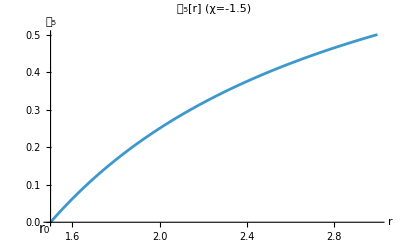

This restriction on the domain of 𝔇_5 is the 6D_1 analog of RCPC.

r_0 = -χ is the 'pinch' point:

• 𝔇_5(r_0) = 0.

• For χ < 0

✓ r_0 > 0

✓ the 6D_1 RCPC domain of r is restricted to r > r_0.

✓ As r→r_0 from above, 𝔇_5→0.

• For χ > 0, 𝔇_5 > 0 and so there is no domain restriction.

Analogous to the original KK bubble, the radial line element for this solution is

ds^2 = 1/(SubscriptBox[𝔇, 5][r]) dr^2 + 𝔇_5[r] p_5^2 dψ_5^2

This is a good time to introduce some vocabulary.

The full 6D spacetime contains 6 parameters, (t,r,θ,ϕ,ψ_4,ψ_5) and has an associated line element. The portion of the line element involving 3-space, (r,θ,ϕ) is called the base line element. Any other portion of the line element, such as the (r,ψ_5) line element, above, is referred to as a transverse line element.

In flat space, ds^2 = dr^2; i.e., the radial distance r equals the proper distance s. In curved space, they are not the same. Hence, to check whether the ψ_5 circle shrinks smoothly down to zero, we have to use the proper distance, s.

𝔇_5[r] p_5^2 is the square of the proper radius. So, our plan is to express √(SubscriptBox[𝔇, 5][r])p_5, the proper radius, in terms of s, and then to examine the proper circumference, 2π√(SubscriptBox[𝔇, 5][r])p_5.

As r→r_0, the ψ_5-circle circumference 2π√(SubscriptBox[𝔇, 5][r])p_5 shrinks down to zero. This is the bubble: the curled ψ_5-direction pinches off completely at r=r_0. As r moves away from r_0, spacetime continues outward.

Notice that as r→r_0, 𝔇_5→0, the dr^2/𝔇_5 term in ds^2 gets large and the 𝔇_5p_5^2dψ_5^2 term gets small, so that ds^2 ≈ dr^2/(SubscriptBox[𝔇, 5][r]) = dr^2/(1 + FractionBox[χ, r]). This is the metric we use to determine whether the pinch has a sharp point or is smooth.

The plots below help visualize the pinch. In the plots, √𝔇_5p_5 are the 
proper radii of the horizontal slices for various r-values. The upper plots 
show 2D cross-sections of the height of the surface vs proper radii. 
The lower plots revolve the upper plots to form surfaces of revolution in 
ordinary 3-space.

With χ=-p_5/2 the bottom is rounded (smooth); with χ=-p_5 it comes to a
sharp point (a cone). The claim below show that χ=-p_5/2 is the only value
that gives a smooth bottom. (Note: the plot uses p_5=1.)

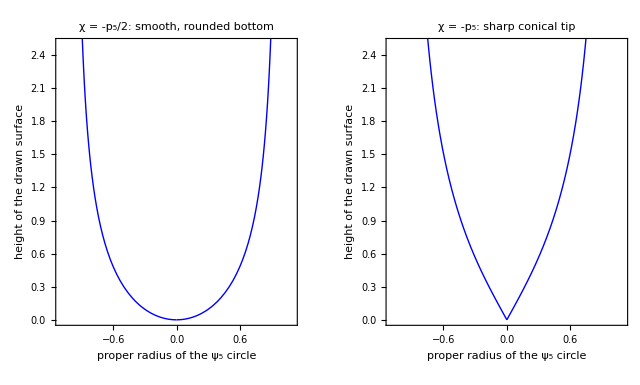

-Graphics-

Claim: smoothness of the pinch places a constraint on χ: χ = -p_5/2

⇒  𝔇_5[r] = 1 + χ/r = 1 - p_5/(2  r).

Proof of claim:

Slope of the tangent line of 𝔇_5 at r_0 is

m = 𝔇_5'(r_0) = -χ/r^2|_r_0 = -χ/(-χ)^2 = -1/χ.

For r near r_0, the tangent line is a 1st order approximation to 𝔇_5.

Set r ≡ r_0 + δ_r for r near to r_0. Since 𝔇_5[r_0]=0, using y-y_0=m(x-x_0) we get,

𝔇_5[r] = 𝔇_5[r]-𝔇_5[r_0] ≈ m(r-r_0) = m δ_r.

⇒ ds ≈ dr/(√(SubscriptBox[𝔇, 5][r])) ≈ dr/(√(m SubscriptBox[δ, r]))

⇒  s ≈ ∫_r_0^r 1/(√(m SubscriptBox[δ, ρ]))ⅆρ = ∫_r_0^r 1/(√(m (ρ - SubscriptBox[r, 0])))ⅆρ = (2 √(m (r-r_0)))/m = 2√(δ_r/m)

⇒ δ_r ≈ (m s^2)/4

⇒ 𝔇_5(r) ≈ m δ_r = (m^2 s^2)/4

We have expressed 𝔇_5 in terms of proper distance, s.

We use this to determine the ψ_5 circle's proper physical circumference.

Recall from above that √(1+χ/r) p_5 is the proper physical radius for the ψ_5 circle.

In terms of s (rather than r),

Proper radius = √(1+χ/r) p_5 ≈ 1/2 m s p_5

Since ψ_5 sweeps its full range of 2π, the actual physical circumference is

Proper circumference = 2π Proper radius = m π s p_5

If the circumference doesn't equal 2πs exactly, the point isn't smooth:

• Less than 2πs is a sharp, cone-like point (a deficit angle)

• More than 2πs is a saddle-like excess.

Smoothness requires the circumference to equal exactly 2πs.

We now apply the smoothness constraint:

m π s p_5 = 2 π s

⇒  χ = -1/m = -p_5/2

This concludes proof of the claim.

Notes

(1) To claim smoothness, the full ds^2 line element involving t, r, θ, ϕ, ψ_4, and ψ_5 must be considered. The transverse line element used to prove the claim involves just r and ψ_5. However since there are no off-diagonal metric terms g_μν, there is no mixing of different directions. Consequently, the entire 6D spacetime is smooth if the transverse space is.

(2) The χ/r term is replaced in the 𝔇_5(r) pattern by -p_5/(2  r) because χ is no longer a free constant.

(3) p_5, by contrast, remains a free constant, as does p_4.

d:  Free-gauge GRW

The table below shows the GRW solution, obtained in Section a, and the FG GRW

solution we are about to obtain. It also provides comparison to prior cases.

|  | 4D | 5D | 6D_1
GRW | Constraints | None | None | Λ>0, k=0
 | KK-bubbleCon-straints(optional) | n/a | χ=r_0(-1+kr_0^2)
where
r_0=(∓1 + SqrtBox[1 + 3 k SubsuperscriptBox[p, 4, 2]])/(3  k SubscriptBox[p, 4])
and k≥-1/(3 SuperscriptBox[SubscriptBox[p, 4], 2]) | χ=-p_5/2
 | 𝒜 | 𝒜(t)=c^2 | 𝒜(t)=c^2 | 𝒜(t)=c^2
 | Β | 1/(1-kr^2) | 1/𝔇_4 | 1/𝔇_5
 | ℭ | 1 | 1 | 1
 | 𝔇_4 |  | 1-k r^2+χ/r | 1
 | 𝔇_5 |  |  | 1-k r^2+χ/r
FG
GRW | 𝒜 | (3 (ȧ)^2)/(-3 k+a^2 Λ) | (4 (ȧ)^2)/(-4 k+a^2 Λ) | (5 (ȧ)^2)/(-5 k+a^2 Λ)
 | Β | (2 ℭ+r ℭ')^2/(4 ℭ (1-k r^2 ℭ)) | (2 ℭ+r ℭ')^2/(4 ℭ𝔇_4) | (2 ℭ+r ℭ')^2/(4 ℭ𝔇_5)
 | ℭ | ℭ (free) | ℭ (free) | ℭ (free)
 | 𝔇_4 |  | 1-k r^2 ℭ+χ/(r √ℭ) | 1
 | 𝔇_5 |  |  | 1-k r^2 ℭ+χ/(r √ℭ)

Notes:

• 𝒜(t) = c^2 is the Friedmann Continuity Equation

✓ The solution to the equation is the a(t) formula from Section b

• The two constraint rows display restrictions on parameter constants

✓ Due to the field equations

✓ Due to KK-bubble smoothness

• By contrast, domain restrictions on r (RCPC and its analogs) are not

displayed as constraints

• FG GRW has the same constraints (both rows) as GRW

The 6D Free-gauge GRW results were obtained from GRW by using the 5D pattern:

𝒜: Replace c^2 by 𝒜 from the 6D GRW equations

Β: Replace r → r√ℭ and multiply result by (2ℭ+r ℭ')^2/(4ℭ)

ℭ: Replace 1 by free parameter ℭ

𝔇_4: Replace r by r√ℭ (nothing to replace)

𝔇_5 is new, so there is no established pattern. What works is simply

𝔇_5: Replace r by r√ℭ

The line element is

ds^2 = (5 (ȧ[t])^2)/(Λ a[t]^2) dt^2 - (a[t]^2 (2 ℭ[r]+r ℭ'[r])^2)/(4 (1-p_5/(2 r √ℭ[r])) ℭ[r]) dr^2 - r^2 a[t]^2 ℭ[r] dθ^2 - r^2 a[t]^2 Sin[θ]^2 ℭ[r] dϕ^2
 - a[t]^2 p_4^2 dψ_4^2 - a[t]^2 p_5^2 (1-p_5/(2 r √ℭ[r])) dψ_5^2

Confirming:

R_00:  Λ = Λ

R_01:  0 = 0

R_02:  0 = 0

R_03:  0 = 0

R_04:  0 = 0

R_05:  0 = 0

R_11:  Λ = Λ

R_12:  0 = 0

R_13:  0 = 0

R_14:  0 = 0

R_15:  0 = 0

R_22:  Λ = Λ

R_23:  0 = 0

R_24:  0 = 0

R_25:  0 = 0

R_33:  Λ = Λ

R_34:  0 = 0

R_35:  0 = 0

R_44:  Λ = Λ

R_45:  0 = 0

R_55:  Λ = Λ

e: The Vacuum Friedmann Equations

Plugging 𝒜, Β, ℭ, and 𝔇_4 (but not a) from the GRW solution into the field equations yields:

R_00:  (5 ä)/(a c^2) = Λ

R_11:  (4 (ȧ)^2)/(a^2 c^2)+(ä)/(a c^2) = Λ

R_22:  (4 (ȧ)^2)/(a^2 c^2)+(ä)/(a c^2) = Λ

R_22 is redundant, the same as R_11.

The Friedmann continuity and acceleration equations, respectively, are the following pair of equations generated by algebraic manipulation of R_00 and R_11:

-1/20R_00+1/4 R_11:  (ȧ)^2/(a^2 c^2) = Λ/5

1/6 R_00+1/6 R_11:  (2 (ȧ)^2)/(3 a^2 c^2)+(ä)/(a c^2) = Λ/3

As pointed out earlier, 𝒜(t) = c^2 is simply a rearrangement of the continuity equation. Since the a(t) formula in Part a is the result of solving 𝒜(t) = c^2, the 4-branch a(t) formula is also the solution to the Friedmann equations.

```mathematica
(* Use Print statements and then view results in the output, not in this code *)

(* lhs and rhs (below) set field equations to express 
         Subscript[R, μν]/Subscript[g, μν] = Λ if Subscript[g, μν]≠0 
  and   Subscript[R, μν] = 0   otherwise 
   lhs uses Expand[Simplify]. lhsF uses Expand[FullSimplify]*)
lhs[μ_,ν_]:=Module[{leftside},
If[g[μ,ν]===0,
leftside =R[μ,ν],leftside=xS[R[μ,ν]/g[μ,ν]]];leftside];

lhsF[μ_,ν_]:=Module[{leftside},
If[g[μ,ν]===0,
leftside =R[μ,ν],leftside=xF[R[μ,ν]/g[μ,ν]]];leftside];

rhs[μ_,ν_]:=Module[{rightside},
If[g[μ,ν]===0,
rightside =Λ g[μ,ν],rightside=Λ];rightside];

Print[];
Print["6D_1 is the Case where the two curled dimensions form a torus, T^2, the product"];
Print["of two circles. That is, T^2 = S^1xS^1."];

Print[];
Print["Note. T^2 is homogeneous but not isotropic. Thus, the solution is expected to have more free parameters than the 6D_2 case where the compact curled space is a 2-sphere, S^2."];

Print[];
Print["Notation and Setup:"];
Β[r_]=1/Subscript[𝔇, 5][r];

ℭ[r_]=1;
k=0;

Print[];
Print[caseMsg/.rulesDot];

Print[];
Print["Lambda Vacuum Equations:  The equations are R_μν = Λ g_μν. They are expressed as R_μν/g_μν = Λ when g_μν ≠ 0, and R_μν = 0 when g_μν = 0. The g_μν matrix used is a diagonal matrix. Since off-diagonal R_μν equations rarely appear, almost all the equations are expressed by dividing out g_μν."];

Print[];
Print["GRW Equations: An exact solution to the Λ vacuum field equations that has (1) free parameter a, (2) ℭ = 1, and (3) parameter 𝒜 such that 𝒜(t) = c^2 is the Friedmann Continuity Equation (which generates the a(t) formula)."];

Print[];
Print["FG GRW Equations: An exact solution to the Λ vacuum field equations that has (1) free parameters a and ℭ, and (2) parameter 𝒜 such that 𝒜(t) = c^2 is the Friedmann Continuity Equation."];

Print[];
Print["a:  GRW Equations"];
Subscript[𝔇, 4][r_]=1;

Print["The line element above shows our initial assumptions. It explicitly shows"];
Print["     a(t) is a free parameter,"];
Print["     A(t,r) is a function of t and r,"];
Print["     Β(r) = 1/𝔇_5,"];
Print["     ℭ(r) = 𝔇_4(r) = 1 ,"];
Print["and  𝔇_5(r) is a function of r."];

Print[];
Print["Approach Overview:"];
Print["  • Like 5D, it is too difficult to solve for FG GRW first, so we"];
Print["    begin with GRW."];
Print["    ✓ By letting ℭ(r) = 1, the equations are simplified and are solvable."];
Print["  • The starting assumptions were derived in the appendix,"];
Print["    which is a separate notebook."];
Print["    ✓ Initially, parameters k, A, Β, 𝔇_4, and 𝔇_5 were free parameters."];
Print["    ✓ An intermediate solution was found that included two branches."];
Print["    ✓ Branch 2 led to a dead end."];
Print["    ✓ We investigate Branch 1 now."];
Print["    ✓ In Branch 1, k, Β, and 𝔇_4 are no longer free and independent:"];
Print["      ◦ Β = 1/𝔇_5"];
Print["      ◦ 𝔇_4 = 1"];
Print["      ◦ Curvature k = 0"];

Print[];
Print["In summary, we continue the Appendix investigation from the point where:"];
Print["     k = 0,"];
Print["     a(t) is not constant,"];
Print["     A(t,r) is a function of t and r,"];
Print["     Β(r) = 1/(SubscriptBox[𝔇, 5][r]), both strictly functions of r (or constants),"];
Print["     ℭ(r) = 𝔇_4[r] = 1."];

Print[];
Print["The initial Lambda field equations are:"];
For[μ=dimL,μ≤dimH,μ++,For[ν=μ,ν≤dimH,ν++,
If[(μ==ν||(μ≠ν&&!lhs[μ,ν]===0)),
Print[Subscript["R",Row[{μ,ν}]],":  ",lhs[μ,ν]/.rulesDisp," = ",rhs[μ,ν]]]]];

Print[];
Print["R_33 is redundant, the same as R_22."];
Print["Since a(t) ≠ constant, from R_01 we get that"];
Print["     A(t,r) = 𝒜(t),  a new unknown, strictly a function of t, which again tells"];
Print["     us that A(t,r) cannot be a function of r."];
A[t_,r_]=𝒜[t];

Print[];
Print["R_01 is eliminated, and the remaining equations become"];
For[μ=dimL,μ≤dimH,μ++,If[!μ==3,Print[Subscript["R",Row[{μ,μ}]],":  ",lhs[μ,μ]/.rulesDisp," = ",rhs[μ,μ]]]];


𝒜[t_]=DSolveValue[lhs[0,0]==rhs[0,0],𝒜[t],t]/.C[1]->-k;
Asave=𝒜[t];

Print[];
Print["R_55 is now redundant, the same as R_11."];
Print["We can immediately find 𝒜 from R_00:"];
Print["     𝒜(t) =",𝒜[t]/.rulesDot,"  where the constant of integration, k, has been set to zero (per assumptions)."];

Print[];
Print["R_00 is eliminated, and the remaining equations become"];
For[μ=1,μ≤4,μ++,If[!μ==3,
Print[Subscript["R",Row[{μ,μ}]],":  ",lhs[μ,μ]/. rulesDisp," = ",rhs[μ,μ]]]];

Subscript[𝔇, 5][r_]=DSolveValue[lhs[2,2]-rhs[2,2]==0,Subscript[𝔇, 5][r],r]/.C[1]->χ;

Print[];
Print["R_44 is an identity, and we can solve R_22 for 𝔇_5:"];
Print["     𝔇_5(r) = ",Subscript[𝔇, 5][r],"  where χ is a constant of integration."]

Print[];
Print["This satisfies remaining equation"];
For[μ=1,μ≤1,μ++,
Print[Subscript["R",Row[{μ,μ}]],":  ",lhs[μ,μ]/. rulesDisp," = ",rhs[μ,μ]]];

Print[];
Print["All of the equations are satisfied, curvature k = 0,"];
Print["and the GRW solution is"];
Print["     A(t,r) = 𝒜(t) = ",𝒜[t]/.rulesDot," = c^2  where Λ > 0"];
Print["     Β(r) = 1/(SubscriptBox[𝔇, 5][r]),"];
Print["     ℭ(r) = ",ℭ[r],","];
Print["     𝔇_4(r) = ",Subscript[𝔇, 4][r],","];
Print["     𝔇_5(r) = ",Subscript[𝔇, 5][r],"  where χ is a constant of integration,"];

Print["and line element"];
Print["     ",lineElem/.𝒜[t]->c^2];

(*Print[];
Print["Confirming:"];
For[μ=dimL,μ≤dimH,μ++,For[ν=μ,ν≤dimH,ν++,
Print[Subscript["R",Row[{μ,ν}]],":  ",lhs[μ,ν]/. rulesDisp," = ",rhs[μ,ν]]]];*)

Print[];
Print["Notes:"];Print["  • Radii p_4 and p_5 remain completely free and independent of each other."];
Print["    ✓ The two radii of the torus need not be the same size. "];
Print["    ✓ The aspect ratio p_4/p_5 is a genuine 'modulus' of the solution:"];
Print["        ◦ It is a flat direction, undetermined by the vacuum-Λ field equations alone."];
Print["    ✓ This is the same phenomenon as the radion/moduli-stabilization problem"];
Print["      we see in Kaluza–Klein compactifications."];

Print[];
Print["b:  Solve 𝒜(t) = c^2 to find a(t)"];

Print[];
Print["Solving ",𝒜[t]/.rulesDot," = c^2 yields"]; 
at1=a[t]/.PowerExpand[Last[DSolve[g[0,0]==c^2,a[t],t]]/.C[1]->α];
Print["     a(t) = ",at1/.E^x_->E^Row[{"±",x}],"  where α > 0 is a constant of integration and Λ > 0."];

Print[];
Print["c:  Kaluza-Klein (KK) bubble-of-nothing"];

Print[];
Print["Case 6D_1 has two curled circles, parameterized by ψ_4 and ψ_5."];
Print["  • The circles begin at ψ_μ=0. Each winds around the circumference of a circle"];
Print["    of radius p_μ and arrives back at the starting point at ψ_μ=2π."];
Print["  • The circles thus have period 2π."];

Print[];Print["The GRW solution 𝔇_5(r) = 1 + χ/r ties the ψ_5 circle to r, even though they were initially unrelated. There is no such tie between the ψ_4 circle and r because 𝔇_4(r) = 1."];

Print[];
Print["Define r_0 ≡ -χ."];Print["In order for 𝔇_5(r) = 1/Β[r] to be positive, we must have r > r_0."];

χ=-1.5;
Print[];
Print["The sample 𝔇_5 plot below (for χ=-1.5, r_0=1.5) helps visualize the domain of r."];

Print[];
Print[Plot[Subscript[𝔇, 5][r],{r,-χ,-2χ},AxesLabel->{Style["r",12],Style[Subscript[𝔇, 5],10]},PlotRangeClipping->False,ImagePadding->{{60,30},{40,10}},PlotLabel->Style["𝔇_5[r]   (χ=-1.5)",12],Epilog->{Text[Style[Subscript[r, 0],14],{-χ,0},{1.4,1.2}]}]];
Clear[χ]

Print[];
Print["This restriction on the domain of 𝔇_5 is the 6D_1 analog of RCPC."];

Print[];
Print["r_0 = -χ is the 'pinch' point:"];
Print["     • 𝔇_5(r_0) = 0."];
Print["     • For χ < 0"];
Print["       ✓ r_0 > 0"];
Print["       ✓ the 6D_1 RCPC domain of r is restricted to r > r_0."];
Print["       ✓ As r→r_0 from above, 𝔇_5→0."];
Print["     • For χ > 0, 𝔇_5 > 0 and so there is no domain restriction."];

Print[];
Print["Analogous to the original KK bubble, the radial line element for this solution is"];
Print["     ds^2 = 1/(SubscriptBox[𝔇, 5][r]) dr^2 + 𝔇_5[r] p_5^2 dψ_5^2"];

Print[];
Print["This is a good time to introduce some vocabulary."];
Print["The full 6D spacetime contains 6 parameters, (t,r,θ,ϕ,ψ_4,ψ_5) and has an associated line element. The portion of the line element involving 3-space, (r,θ,ϕ) is called the base line element. Any other portion of the line element, such as the (r,ψ_5) line element, above, is referred to as a transverse line element."];

Print[];
Print["In flat space, ds^2 = dr^2; i.e., the radial distance r equals the proper distance s. In curved space, they are not the same. Hence, to check whether the ψ_5 circle shrinks smoothly down to zero, we have to use the proper distance, s."];

Print[];
Print["𝔇_5[r] p_5^2 is the square of the proper radius. So, our plan is to express √(SubscriptBox[𝔇, 5][r])p_5, the proper radius, in terms of s, and then to examine the proper circumference, 2π√(SubscriptBox[𝔇, 5][r])p_5."];

Print[];
Print["As r→r_0, the ψ_5-circle circumference 2π√(SubscriptBox[𝔇, 5][r])p_5 shrinks down to zero. This is the bubble: the curled ψ_5-direction pinches off completely at r=r_0. As r moves away from r_0, spacetime continues outward."];

Print[];
Print["Notice that as r→r_0, 𝔇_5→0, the dr^2/𝔇_5 term in ds^2 gets large and the 𝔇_5p_5^2dψ_5^2 term gets small, so that ds^2 ≈ dr^2/(SubscriptBox[𝔇, 5][r]) = dr^2/(1 + FractionBox[χ, r]). This is the metric we use to determine whether the pinch has a sharp point or is smooth."];

Print[];
Print["The plots below help visualize the pinch. In the plots, √𝔇_5p_5 are the 
proper radii of the horizontal slices for various r-values. The upper plots 
show 2D cross-sections of the height of the surface vs proper radii. 
The lower plots revolve the upper plots to form surfaces of revolution in 
ordinary 3-space. "];

Print[];
Print["With χ=-p_5/2 the bottom is rounded (smooth); with χ=-p_5 it comes to a
sharp point (a cone). The claim below show that χ=-p_5/2 is the only value
that gives a smooth bottom. (Note: the plot uses p_5=1.)"];
Print[];

p5 = 1;  (* circle radius; the plot ranges below assume p5 = 1 *)
Subscript[p, 5]=1;
χ=chi;

height[chi_] := Module[{r0 = -chi},
   NDSolveValue[{z'[u] == 2 Sqrt[r0 + u^2] Sqrt[1 - p5^2 chi^2/(4 (r0 + u^2)^4)],
     z[0] == 0}, z, {u, 0, 2}]];

radius[chi_, u_] := p5 u/Sqrt[-chi + u^2];

(* 2D cross-sections, side by side *)
profile[chi_, label_] := With[{zf = height[chi]},
   ParametricPlot[{{radius[chi, u], zf[u]}, {-radius[chi, u], zf[u]}}, {u, 0, 2},
    PlotStyle -> Directive[Blue, Thick], AspectRatio -> Automatic,
    PlotRange -> {{-1.1, 1.1}, {0, 2.5}}, Frame -> True, Axes -> False,
    FrameLabel -> {"proper radius of the ψ_5 circle", "height of the drawn surface"},
    PlotLabel -> label, ImageSize -> 330]];

Print[GraphicsRow[{profile[-p5/2, "χ = -p_5/2: smooth, rounded bottom"],
  profile[-p5, "χ = -p_5: sharp conical tip"]}]];

(* Optional: the same two surfaces in 3D *)
surface[chi_, label_] := With[{zf = height[chi]},
   ParametricPlot3D[{radius[chi, u] Cos[t], radius[chi, u] Sin[t], zf[u]},
    {u, 0, 2}, {t, 0, 2 Pi}, PlotRange -> {{-1.1, 1.1}, {-1.1, 1.1}, {0, 2.5}},
    BoxRatios -> Automatic, Mesh -> 12, PlotLabel -> label, ImageSize -> 330]];

Print[GraphicsRow[{surface[-Subscript[p, 5]/2, "χ = -p_5/2"], surface[-Subscript[p, 5], "χ = -p_5"]}]];
Subscript[p, 5]=.;
Clear[χ]

Print[];
Print["Claim: smoothness of the pinch places a constraint on χ: χ = ",-1/2 Subscript[p, 5]];
Print[" ⇒  𝔇_5[r] = 1 + χ/r = 1 - p_5/(2  r)."];

Print[];
Print["Proof of claim:"];
Print["   Slope of the tangent line of 𝔇_5 at r_0 is"];
Print["      m = 𝔇_5'(r_0) = -χ/r^2|_r_0 = -χ/(-χ)^2 = -1/χ."];
Print["   For r near r_0, the tangent line is a 1st order approximation to 𝔇_5."];
Print["   Set r ≡ r_0 + δ_r for r near to r_0. Since 𝔇_5[r_0]=0, using y-y_0=m(x-x_0) we get,"];
Print["      𝔇_5[r] = 𝔇_5[r]-𝔇_5[r_0] ≈ m(r-r_0) = m δ_r."];
Print["    ⇒ ds ≈ dr/(√(SubscriptBox[𝔇, 5][r])) ≈ dr/(√(m SubscriptBox[δ, r]))"];
Print["    ⇒  s ≈ ∫_r_0^r 1/(√(m SubscriptBox[δ, ρ]))ⅆρ = ∫_r_0^r 1/(√(m (ρ - SubscriptBox[r, 0])))ⅆρ = ",∫_Subscript[r, 0]^r 1/(√(m (ρ-Subscript[r, 0])))ⅆρ," = 2√(δ_r/m)"];
Print["    ⇒ δ_r ≈ ",1/4 m s^2];
Print["    ⇒ 𝔇_5(r) ≈ m δ_r = ",1/4 m^2 s^2];
Print["    We have expressed 𝔇_5 in terms of proper distance, s."];
Print["    We use this to determine the ψ_5 circle's proper physical circumference."];

Print["    Recall from above that ",√(Subscript[𝔇, 5][r])Subscript[p, 5]," is the proper physical radius for the ψ_5 circle. "];
Print["    In terms of s (rather than r),"];
Print["       Proper radius = ",√(Subscript[𝔇, 5][r])Subscript[p, 5]," ≈ ",1/2 m Subscript[p, 5] s];

Print[];
Print["    Since ψ_5 sweeps its full range of 2π, the actual physical circumference is"];
Print["       Proper circumference = 2π Proper radius = ",π m Subscript[p, 5] s];

Print[];
Print["    If the circumference doesn't equal 2πs exactly, the point isn't smooth:"];
Print["    • Less than 2πs is a sharp, cone-like point (a deficit angle)"];
Print["    • More than 2πs is a saddle-like excess."];
Print["    Smoothness requires the circumference to equal exactly 2πs."];

Print[];
Print["    We now apply the smoothness constraint:"];
Print["       ",π m Subscript[p, 5] s," = ",2π s];
Print["    ⇒  ",χ," = ",-1/m," = ",-Subscript[p, 5]/2];
Print["    This concludes proof of the claim."];

Print[];
Print["Notes"];
Print["(1) To claim smoothness, the full ds^2 line element involving t, r, θ, ϕ, ψ_4, and ψ_5 must be considered. The transverse line element used to prove the claim involves just r and ψ_5. However since there are no off-diagonal metric terms g_μν, there is no mixing of different directions. Consequently, the entire 6D spacetime is smooth if the transverse space is."];
Print["(2) The χ/r term is replaced in the 𝔇_5(r) pattern by -p_5/(2  r) because χ is no longer a free constant."];
Print["(3) p_5, by contrast, remains a free constant, as does p_4."];


Print[];
Print["d:  Free-gauge GRW"]
Clear[ℭ,k,χ]  (* Must clear parameters so table can include lower dimensions *)

𝒜[t_]=Asave;
Subscript[𝔇, 5][r_]=1-k r^2 ℭ[r]-Subscript[p, 5]/(2r √ℭ[r]); (* k is zero *)
Β[r_]=(2ℭ[r]+ r ℭ'[r])^2/(4ℭ[r]Subscript[𝔇, 5][r]);

Print[];
Print["The table below shows the GRW solution, obtained in Section a, and the FG GRW"];
Print["solution we are about to obtain. It also provides comparison to prior cases."];

Print[];
Print["  ",
 Grid[
  {
   {"", "", Item[Style["4D", Blue, Bold], Alignment -> Center],
     Item[Style["5D", Blue, Bold], Alignment -> Center], Item[Style["6D_1", Blue, Bold], Alignment -> Center]},

      {Item[Style["GRW", Magenta, Bold], Alignment -> {Center, Center}],
     Style["Constraints",Small,Brown,Bold], "None","None","Λ>0, k=0"},
{SpanFromAbove,Style[Row[{"KK-bubble","Con-","straints","(optional)"}],Small,Brown,Bold],"n/a",Column[{"χ=r_0(-1+kr_0^2)","where","r_0=(∓1 + SqrtBox[1 + 3 k SubsuperscriptBox[p, 4, 2]])/(3  k SubscriptBox[p, 4])","and k≥-1/(3 SuperscriptBox[SubscriptBox[p, 4], 2])"}],"χ=-p_5/2"},{SpanFromAbove,Style["𝒜",Larger,Blue,Bold],"𝒜(t)=c^2","𝒜(t)=c^2","𝒜(t)=c^2"},
   {SpanFromAbove,Style["Β",Larger,Blue,Bold], 1/(1 - kr^2),1/Subscript[𝔇, 4],1/Subscript[𝔇, 5]},
   {SpanFromAbove,Style["ℭ",Larger,Blue,Bold], 1, 1,1},
   {SpanFromAbove,Style["𝔇_4",Larger,Blue,Bold], "",
     1 - k r^2 + χ/r,1},
  {SpanFromAbove,Style["𝔇_5",Larger,Blue,Bold], "","",
    1-k r^2+χ/r},

   
   {Item[Style[Column[{"FG","GRW"}], Magenta, Bold], Alignment -> {Center, Center}],
      Style["𝒜",Larger,Blue,Bold],3 (ȧ)^2/(-3 k + Λ a^2), 4 (ȧ)^2/(-4 k + Λ a^2),5 (ȧ)^2/(-5k+Λ a^2)},
   {SpanFromAbove, Style["Β",Larger,Blue,Bold], (2 ℭ + r ℭ')^2/(4 ℭ (1 - k r^2 ℭ)),
     (2 ℭ + r ℭ')^2/(Row[{4 ℭ ,Subscript[𝔇, 4]}]),Row[{(2 ℭ + r ℭ')^2/(Row[{4 ℭ ,Subscript[𝔇, 5]}])}]},
   {SpanFromAbove,Style["ℭ",Larger,Blue,Bold] , "ℭ (free)","ℭ (free)", "ℭ (free)"},
   {SpanFromAbove,Style["𝔇_4",Larger,Blue,Bold], "",1 - k r^2 ℭ + χ/(r √ℭ),1},
{SpanFromAbove,Style["𝔇_5",Larger,Blue,Bold], "","",1-k r^2 ℭ+χ/(r √ℭ)}
  },
  Frame -> All,ItemSize->{{4,5,6,8,9},Automatic},(* col widths *)
  Alignment -> Left,
  Spacings -> {2, 1.5}
 ]];

Print[];
Print["Notes:"];
Print["  • 𝒜(t) = c^2 is the Friedmann Continuity Equation"];
Print["    ✓ The solution to the equation is the a(t) formula from Section b"];
Print["  • The two constraint rows display restrictions on parameter constants"];
Print["    ✓ Due to the field equations"];
Print["    ✓ Due to KK-bubble smoothness"];
Print["  • By contrast, domain restrictions on r (RCPC and its analogs) are not"];
Print["    displayed as constraints"];
Print["  • FG GRW has the same constraints (both rows) as GRW"];

k=0;

Print[];
Print["The 6D Free-gauge GRW results were obtained from GRW by using the 5D pattern:"];
Print["     𝒜: Replace c^2 by 𝒜 from the 6D GRW equations"];
Print["     Β: Replace r → r√ℭ and multiply result by (2ℭ+r ℭ')^2/(4ℭ)"];
Print["     ℭ: Replace 1 by free parameter ℭ"];
Print["     𝔇_4: Replace r by r√ℭ (nothing to replace)"];

Print[];
Print["𝔇_5 is new, so there is no established pattern. What works is simply"];
Print["     𝔇_5: Replace r by r√ℭ"];

Print[];
Print["The line element is"];
Print[lineElem/.rulesDot];

Print[];
Print["Confirming:"];
For[μ=dimL,μ≤dimH,μ++,For[ν=μ,ν≤dimH,ν++,
Print[Subscript["R",Row[{μ,ν}]],":  ",lhs[μ,ν]/. rulesDisp," = ",rhs[μ,ν]]]]

Clear[a];
Print[];
Print["e: The Vacuum Friedmann Equations"];
𝒜[t_]=c^2;  
n=dimH;

Print["Plugging 𝒜, Β, ℭ, and 𝔇_4 (but not a) from the GRW solution into the field equations yields:"];
For[μ=dimL,μ≤dimH,μ++,For[ν=μ,ν≤2,ν++,
If[!(R[μ,ν]===Λ g[μ,ν]),Print[Subscript["R",Row[{μ,μ}]],":  ",lhs[μ,μ]/.rulesKr/. rulesDisp," = ",rhs[μ,μ]]]]];

Print[];
Print["R_22 is redundant, the same as R_11."];

Print["The Friedmann continuity and acceleration equations, respectively, are the following pair of equations generated by algebraic manipulation of R_00 and R_11:"];

lhs01=Expand[-lhs[0,0]/(n(n-1))+lhs[1,1]/(n-1)];
rhs01=-rhs[0,0]/(n(n-1))+rhs[1,1]/(n-1);
Print["     ",-1/(n(n-1)),"R_00+",1/(n-1),"R_11:  ",lhs01/.rulesDisp," = ",rhs01];

lhs01b=Expand[lhs[0,0]/(n+1)+lhs[1,1]/(n+1)];
rhs01b=rhs[0,0]/(n+1)+rhs[1,1]/(n+1);
Print["      ",1/(n+1),"R_00+",1/(n+1),"R_11:  ",lhs01b/.rulesDisp," = ",rhs01b];

Print[];
Print["As pointed out earlier, 𝒜(t) = c^2 is simply a rearrangement of the continuity equation. Since the a(t) formula in Part a is the result of solving 𝒜(t) = c^2, the 4-branch a(t) formula is also the solution to the Friedmann equations."];
```

### Spacetime Geodesic Equations Of Motion

```mathematica
μ=.;ν=.;σ=.;

Print["Geodesic Equations for a free particle with mass in the rotating frame K, corresponding to (1) the initial equations if this is run after initialization of this notebook or (2) the last run Lambda field equations case, above:"];
Print["     ",Style[Row[{("ẍ")^μ," + ",Row[{Subscript[Γ, Row[{ν,σ}]]^μ,("ẋ")^ν,OverDot["x"]^σ}],
" = 0"}],Bold,Blue]];

Print["where ẍ^μ, (ẋ)^ν and (ẋ)^σ are differentiation wrt proper time τ and A' and B' are 
differentiation wrt r. "];

Γdd[μ_,ν_]:=Sum[Γ[μ,ν,γ] 𝓍'[ν] 𝓍'[γ],{γ,dimL,dimH}]; 
gammadd=Table[Γdd[μ,ν],{μ,dimL,dimH},{ν,dimL,dimH}]; 

eqGeo[μ_]:= Sum[Γdd[μ,ν],{ν,dimL,dimH}];
For[μ= dimL,μ≤dimH,μ++,
Print["(",index1,"=",μ,"): ", 
Text[𝓍''[μ]]//.rulesX," + ",xS[eqGeo[μ]]//.rulesX
/.rulesDisp," = 0"]]
```

### Geodesic Equations computations (debug)

```mathematica
Γdd[μ_,ν_]:=Sum[Γ[μ,ν,γ] 𝓍'[ν] 𝓍'[γ],{γ,dimL,dimH}]; 
gammadd=Table[Γdd[μ,ν],{μ,dimL,dimH},{ν,dimL,dimH}]; 
line1="Backup Data: Terms that sum to LHS of equations";
line2="    (not using Einstein summation notation)";
titleT=Column[{line1,line2}];
indexG=Row[{Subscript[Style[Σ,28], index2],Subscript[Γ, Row[{index2, index3}]]^index1,
(ẋ)^index2,(ẋ)^index3}];
column2G=Flatten[gammadd]//.rulesX/.rulesDisp;
table2[titleT,index1,index2,indexG,column21,column22,column2G,numDim]
```